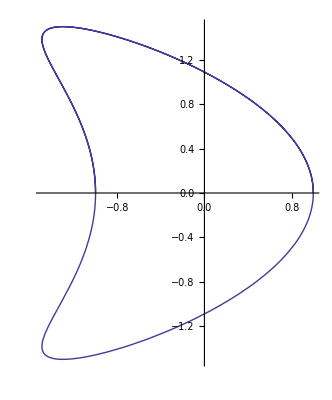

```mathematica
ParametricPlot[{a Cos[t]+0.5b (Cos[2 t]-1),c Sin[ t]}/.{a->1,b->1.3,c->1.5},{t,0,3*π}]
```

```mathematica
A-wigth
D - height
C-offset
ArcTan
```

```mathematica
D[(1.5Sin[t])/(Cos[t]+0.67(Cos[2 t]-1)),t]/.t->π-1e-10
```

-(1.5 Cos[10+e])/(-Cos[10+e]+0.67 (-1+Cos[2 (-10-e+π)]))-(1.5 Sin[10+e] (-Sin[10+e]-1.34 Sin[2 (-10-e+π)]))/(-Cos[10+e]+0.67 (-1+Cos[2 (-10-e+π)]))^2

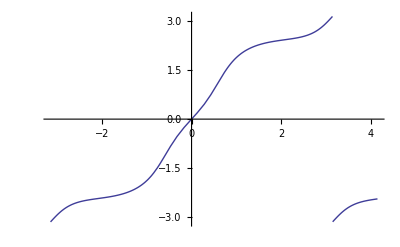

```mathematica
Plot[Arg[Cos[t]+0.67(Cos[2 t]-1)+ⅈ 1.5Sin[t]],{t,-π,π+1}]
```

```mathematica
Cos[2t]==2 Cos[t]^2-1//Simplify
```

True

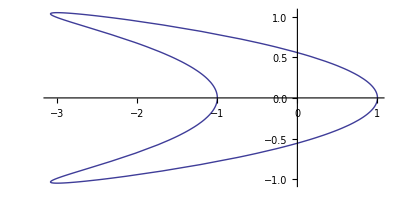

```mathematica
ParametricPlot[{a Cos[t]+b (Cos[t]^2-1),d Sin[ t]}/.{a->1,b->3,c->-0.65,d->1.05},{t,0,2*π}]
```

```mathematica
a Cos[t]+0.5b (Cos[2 t]-1)//TrigReduce
```

-0.5 b+a Cos[t]+0.5 b Cos[2 t]

```mathematica
(Cos[t/2]^2+Sin[t/2]^2)^(1/2)//Simplify
```

1

```mathematica
Sin[t/2+π/4]//TrigExpand
```

Cos[t/2]/(√2)+Sin[t/2]/(√2)

```mathematica
1./√2
```

0.707107

```mathematica
((Cos[t/2]+Sin[t/2])/(√2))^20==0//Reduce
```

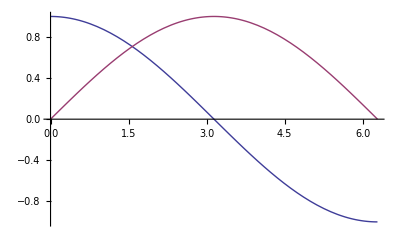

```mathematica
Plot[{Cos[t/2],Sin[t/2]},{t,0,2*π},PlotRange->Full]
```

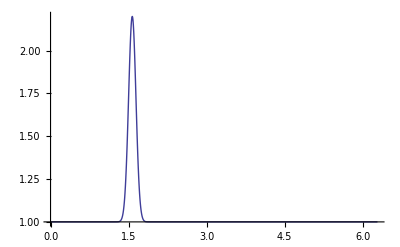

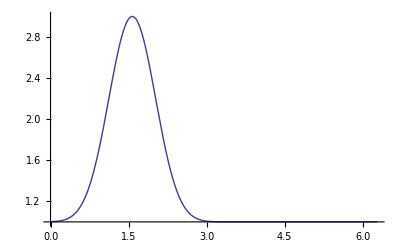

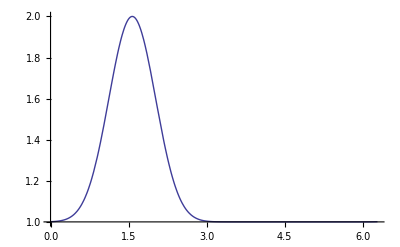

```mathematica
Plot[(1+0.6(1-Tanh[100(t-π)])Sin[t]^200),{t,0,2*π},PlotRange->Full]
Plot[1+2((Sin[t/2]+Cos[t/2])/(√2))^20,{t,0,2*π},PlotRange->Full]
Plot[(1+((Cos[t/2]+Sin[t/2])/(√2))^20),{t,0,2*π},PlotRange->Full]
```

```mathematica
1.8/5 Sin[t](1+((Cos[t/2]+Sin[t/2])/(√2))^200)/.t->3π/4
```

0.254558

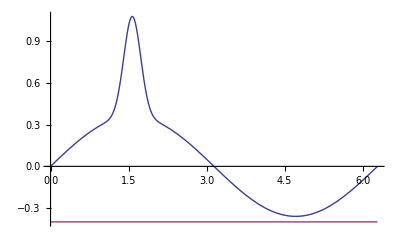

```mathematica
Plot[{1.8/5 Sin[t](1+2((Cos[t/2]+Sin[t/2])/(√2))^150),-0.4},{t,0,2*π},PlotRange->Full]
```

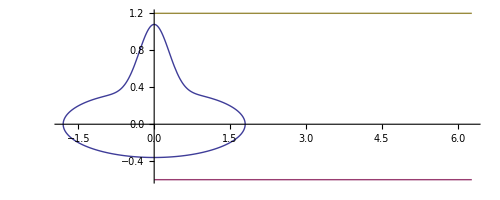

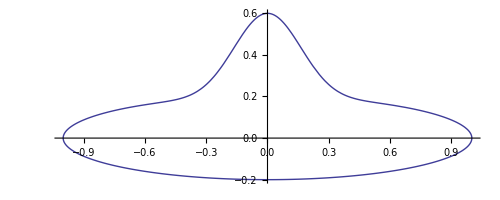

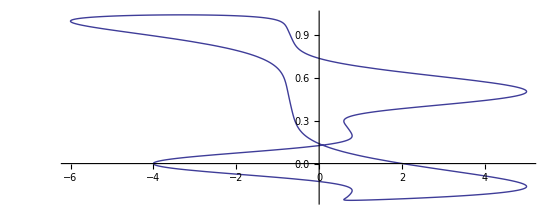

```mathematica
(*ParametricPlot[{Cos[t],1/5 Sin[t](1+2 Sin[t/2+π/4]^200)},{t,0,2*π}]*)
ParametricPlot[{{1.8Cos[t],1.8/5 Sin[t](1+2((Cos[t/2]+Sin[t/2])/(√2))^150)},{t,-0.6},{t,1.2}},{t,0,2*π}]
ParametricPlot[{1Cos[t],1/5 Sin[t](1+2((Cos[t/2]+Sin[t/2])/(√2))^150)},{t,0,2*π}]
ParametricPlot[{1Cos[t]-5 Cos[2t]^5,1/3 Sin[t]+Sin[t/2]^5},{t,0,2*π}]
```

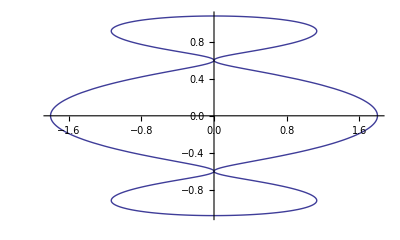

```mathematica
ParametricPlot[{Cos[t]+0.8Cos[5t],Sin[t]+0.08Sin[5t]},{t,0,2π},PlotRange->Full]
```

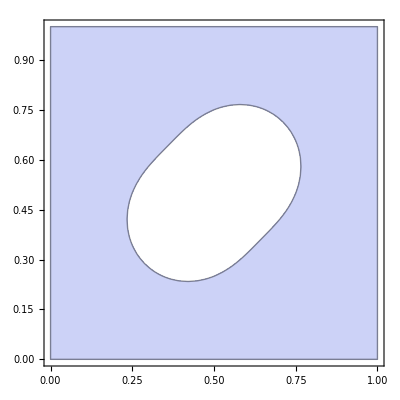

```mathematica
RegionPlot[√((x-Subscript[x, 0])^2+(y-Subscript[y, 0])^2)-(Subscript[r, 0]+ϵ Sin[2Arg[(x-Subscript[x, 0])+ⅈ (y-Subscript[y, 0])]])>0/.{Subscript[x, 0]->0.5,Subscript[y, 0]->0.5,ϵ->0.05,Subscript[r, 0]->0.25},{x,0,1},{y,0,1}]
```

```mathematica
5
```

```mathematica
Cos[t]+Cos[4 t]//FullSimplify
```

Cos[t]+Cos[4 t]

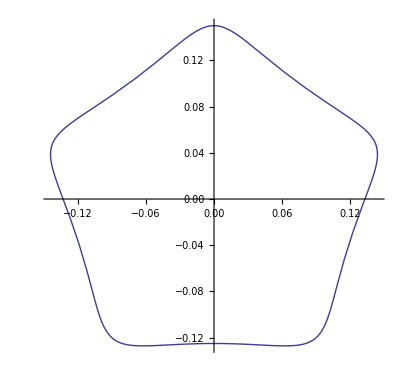

```mathematica
ParametricPlot[1/80{ 11Cos[t]+Sin[4t],11Sin[t]+Cos[4t]},{t,0,2π},PlotRange->Full]
```

```mathematica
7
```

```mathematica
3
```

```mathematica
fx=cos(u)*(abs(cos(1*u/4))^0.5+abs(sin(1*u/4))^0.5)^(-1/0.3)
fy=cos(u)*sin(v)*(abs(cos(1*u/4))^0.5+abs(sin(1*u/4))^0.5)^(-1/0.3)*(abs(cos(5*v/4))^1.7+abs(sin(5*v/4))^1.7)^(-1/0.1)
```

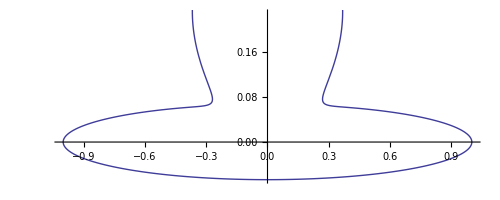

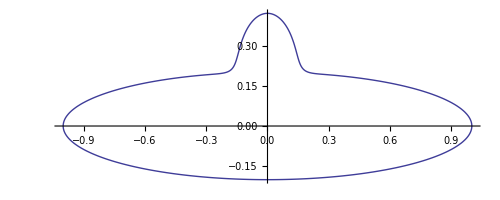

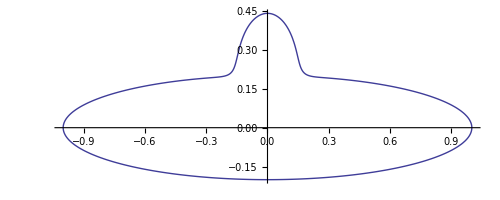

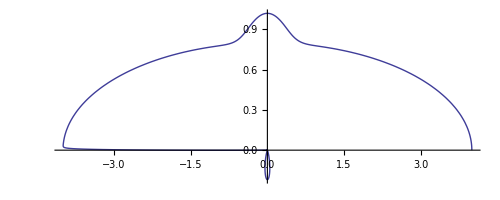

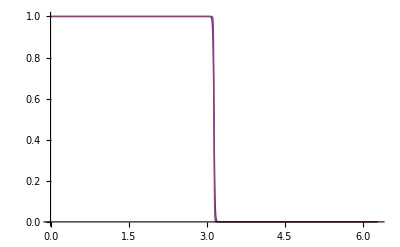

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
ParametricPlot[{Cos[t],1/15 Sin[t]}(1+5((Cos[t/2]+Sin[t/2])/(√2))^500),{t,0,2*π}]
ParametricPlot[{Cos[t],1/5 Sin[t]}(1+1.1(1/(ⅇ^(100(t-π))+1))Sin[t]^200),{t,0,2*π}]
ParametricPlot[{Cos[t],1/5 Sin[t]}(1+0.6(1-Tanh[100(t-π)])Sin[t]^200),{t,0,2*π}]
ParametricPlot[{Cos[t],1/5 Sin[t]}(2(1-Tanh[100(t-π)])+1.1 Sin[t]^200),{t,0,2*π}]
Plot[{1/(ⅇ^(100(t-π))+1),1/2-1/2Tanh[100(t-π)]},{t,0,2*π}]
```

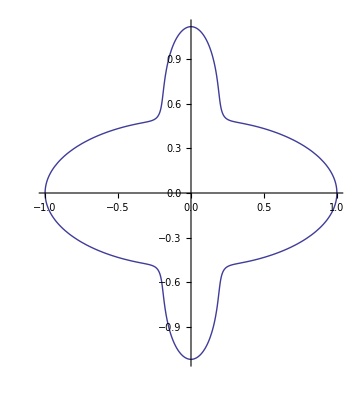

```mathematica
ParametricPlot[{Cos[t],Sin[t]}√((1+4 Sin[t]^40)/(Cos[t]^2+4 Sin[t]^2)),{t,0,2*π}]
```

```mathematica
{Cos[t],1/5 Sin[t]}(1+1.1(1/(ⅇ^(100(t-π))+1))Sin[t]^200)//Simplify
```

{Cos[t] (1+(1.1 Sin[t]^200)/(1+ⅇ^(100 (-π+t)))),1/5 (Sin[t]+(1.1 Sin[t]^201)/(1+ⅇ^(100 (-π+t))))}

```mathematica
Cos[t] Sin[t]^200//FullSimplify
```

Cos[t] Sin[t]^200

```mathematica
1.1(1/(ⅇ^(100(t-π))+1))==1//Reduce
```

ⅇ^(100 t)==2.73927×10^135

```mathematica
f(t) = (1+c sin(t)^p/(d exp(e(t-pi))+1))
x=a cos(t)f(t)
y=b sin(t)f(t)
```

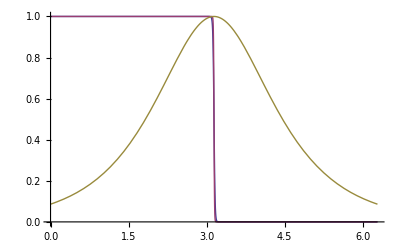

```mathematica
Plot[{1/(ⅇ^(100(t-π))+1),1/2-1/2Tanh[100(t-π)],Sech[ (-π+t)]},{t,0,2*π}]
```

```mathematica
u=.
```

```mathematica
a^2 √a
```

a^(5/2)

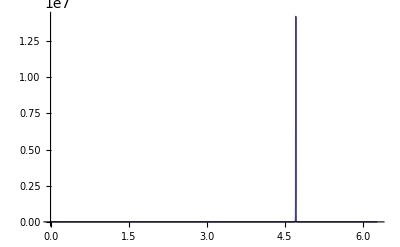

```mathematica
Plot[Cos[π/4+t/a]^2/Sin[π/4+t/a]^2/.a->2,{t,0,2*π},PlotRange->Full]
```

```mathematica
u=(1+c ((Cos[t/a]+Sin[t/a])/(√a))^p)
(**)(*u=(1+a Sin[t/a+π/4]^p)*)
D[u,t]
D[u,{t,2}]
D[u,{t,3}]
D[u,{t,4}]
D[u,{t,5}]
```

1+c ((Cos[t/a]+Sin[t/a])/(√a))^p

(c p ((Cos[t/a]+Sin[t/a])/(√a))^(-1+p) (Cos[t/a]/a-Sin[t/a]/a))/(√a)

c ((p ((Cos[t/a]+Sin[t/a])/(√a))^(-1+p) (-Cos[t/a]/a^2-Sin[t/a]/a^2))/(√a)+((-1+p) p ((Cos[t/a]+Sin[t/a])/(√a))^(-2+p) (Cos[t/a]/a-Sin[t/a]/a)^2)/a)

c ((p ((Cos[t/a]+Sin[t/a])/(√a))^(-1+p) (-Cos[t/a]/a^3+Sin[t/a]/a^3))/(√a)+(3 (-1+p) p ((Cos[t/a]+Sin[t/a])/(√a))^(-2+p) (-Cos[t/a]/a^2-Sin[t/a]/a^2) (Cos[t/a]/a-Sin[t/a]/a))/a+((-2+p) (-1+p) p ((Cos[t/a]+Sin[t/a])/(√a))^(-3+p) (Cos[t/a]/a-Sin[t/a]/a)^3)/a^(3/2))

c ((p ((Cos[t/a]+Sin[t/a])/(√a))^(-1+p) (Cos[t/a]/a^4+Sin[t/a]/a^4))/(√a)+(3 (-1+p) p ((Cos[t/a]+Sin[t/a])/(√a))^(-2+p) (-Cos[t/a]/a^2-Sin[t/a]/a^2)^2)/a+(4 (-1+p) p ((Cos[t/a]+Sin[t/a])/(√a))^(-2+p) (-Cos[t/a]/a^3+Sin[t/a]/a^3) (Cos[t/a]/a-Sin[t/a]/a))/a+(6 (-2+p) (-1+p) p ((Cos[t/a]+Sin[t/a])/(√a))^(-3+p) (-Cos[t/a]/a^2-Sin[t/a]/a^2) (Cos[t/a]/a-Sin[t/a]/a)^2)/a^(3/2)+((-3+p) (-2+p) (-1+p) p ((Cos[t/a]+Sin[t/a])/(√a))^(-4+p) (Cos[t/a]/a-Sin[t/a]/a)^4)/a^2)

c ((p ((Cos[t/a]+Sin[t/a])/(√a))^(-1+p) (Cos[t/a]/a^5-Sin[t/a]/a^5))/(√a)+(10 (-1+p) p ((Cos[t/a]+Sin[t/a])/(√a))^(-2+p) (-Cos[t/a]/a^3+Sin[t/a]/a^3) (-Cos[t/a]/a^2-Sin[t/a]/a^2))/a+(5 (-1+p) p ((Cos[t/a]+Sin[t/a])/(√a))^(-2+p) (Cos[t/a]/a^4+Sin[t/a]/a^4) (Cos[t/a]/a-Sin[t/a]/a))/a+(15 (-2+p) (-1+p) p ((Cos[t/a]+Sin[t/a])/(√a))^(-3+p) (-Cos[t/a]/a^2-Sin[t/a]/a^2)^2 (Cos[t/a]/a-Sin[t/a]/a))/a^(3/2)+(10 (-2+p) (-1+p) p ((Cos[t/a]+Sin[t/a])/(√a))^(-3+p) (-Cos[t/a]/a^3+Sin[t/a]/a^3) (Cos[t/a]/a-Sin[t/a]/a)^2)/a^(3/2)+(10 (-3+p) (-2+p) (-1+p) p ((Cos[t/a]+Sin[t/a])/(√a))^(-4+p) (-Cos[t/a]/a^2-Sin[t/a]/a^2) (Cos[t/a]/a-Sin[t/a]/a)^3)/a^2+((-4+p) (-3+p) (-2+p) (-1+p) p ((Cos[t/a]+Sin[t/a])/(√a))^(-5+p) (Cos[t/a]/a-Sin[t/a]/a)^5)/a^(5/2))

```mathematica
(*u=1+c(1/(d ⅇ^(e(t-π))+1))Sin[t]^p*)
u=1+c Sf[t] Sin[t]^p
D[u,t]
D[u,{t,2}]== (-1+p) p c Sf[t] Cos[t]^2 Sin[t]^(-2+p)+2 c p Cos[t] Sin[t]^(-1+p) Sf'[t]+c Sin[t]^p Sf''[t]-p (u-1)//Simplify
D[u,{t,3}]
D[u,{t,4}]
D[u,{t,5}]
```

1+c Sf[t] Sin[t]^p

c p Cos[t] Sf[t] Sin[t]^(-1+p)+c Sin[t]^p Sf'[t]

True

c Sf[t] ((-2+p) (-1+p) p Cos[t]^3 Sin[t]^(-3+p)-2 (-1+p) p Cos[t] Sin[t]^(-1+p)-p^2 Cos[t] Sin[t]^(-1+p))+3 c ((-1+p) p Cos[t]^2 Sin[t]^(-2+p)-p Sin[t]^p) Sf'[t]+3 c p Cos[t] Sin[t]^(-1+p) Sf''[t]+c Sin[t]^p Sf^(3)[t]

c Sf[t] ((-3+p) (-2+p) (-1+p) p Cos[t]^4 Sin[t]^(-4+p)-3 (-2+p) (-1+p) p Cos[t]^2 Sin[t]^(-2+p)-2 (-1+p)^2 p Cos[t]^2 Sin[t]^(-2+p)-(-1+p) p^2 Cos[t]^2 Sin[t]^(-2+p)+2 (-1+p) p Sin[t]^p+p^2 Sin[t]^p)+4 c ((-2+p) (-1+p) p Cos[t]^3 Sin[t]^(-3+p)-2 (-1+p) p Cos[t] Sin[t]^(-1+p)-p^2 Cos[t] Sin[t]^(-1+p)) Sf'[t]+6 c ((-1+p) p Cos[t]^2 Sin[t]^(-2+p)-p Sin[t]^p) Sf''[t]+4 c p Cos[t] Sin[t]^(-1+p) Sf^(3)[t]+c Sin[t]^p Sf^(4)[t]

c Sf[t] ((-4+p) (-3+p) (-2+p) (-1+p) p Cos[t]^5 Sin[t]^(-5+p)-4 (-3+p) (-2+p) (-1+p) p Cos[t]^3 Sin[t]^(-3+p)-3 (-2+p)^2 (-1+p) p Cos[t]^3 Sin[t]^(-3+p)-2 (-2+p) (-1+p)^2 p Cos[t]^3 Sin[t]^(-3+p)-(-2+p) (-1+p) p^2 Cos[t]^3 Sin[t]^(-3+p)+6 (-2+p) (-1+p) p Cos[t] Sin[t]^(-1+p)+4 (-1+p)^2 p Cos[t] Sin[t]^(-1+p)+4 (-1+p) p^2 Cos[t] Sin[t]^(-1+p)+p^3 Cos[t] Sin[t]^(-1+p))+5 c ((-3+p) (-2+p) (-1+p) p Cos[t]^4 Sin[t]^(-4+p)-3 (-2+p) (-1+p) p Cos[t]^2 Sin[t]^(-2+p)-2 (-1+p)^2 p Cos[t]^2 Sin[t]^(-2+p)-(-1+p) p^2 Cos[t]^2 Sin[t]^(-2+p)+2 (-1+p) p Sin[t]^p+p^2 Sin[t]^p) Sf'[t]+10 c ((-2+p) (-1+p) p Cos[t]^3 Sin[t]^(-3+p)-2 (-1+p) p Cos[t] Sin[t]^(-1+p)-p^2 Cos[t] Sin[t]^(-1+p)) Sf''[t]+10 c ((-1+p) p Cos[t]^2 Sin[t]^(-2+p)-p Sin[t]^p) Sf^(3)[t]+5 c p Cos[t] Sin[t]^(-1+p) Sf^(4)[t]+c Sin[t]^p Sf^(5)[t]

```mathematica
(c d e ⅇ^(e (-π+t)) Sin[t]^p)/((1+d ⅇ^(e (-π+t)))^2)==(d e ⅇ^(e (-π+t)))/(1+d ⅇ^(e (-π+t)))(u-1)//Simplify
(c p Cos[t] Sin[t]^(-1+p))/(1+d ⅇ^(e (-π+t)))==p Cot[t](u-1)
```

True

True

```mathematica
(p Cot[t]+(d e ⅇ^(e (-π+t)))/(1+d ⅇ^(e (-π+t))))//FullSimplify
```

(d e ⅇ^(e t))/(ⅇ^(e π)+d ⅇ^(e t))+p Cot[t]

```mathematica
Cos[t]/Sin[t]
```

Cot[t]

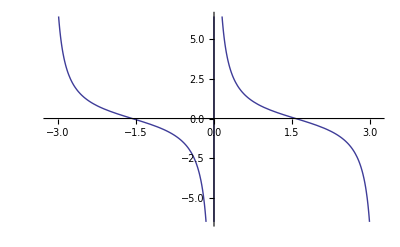

```mathematica
Plot[Cot[t],{t,-π,π}]
```

```mathematica
-4/5+4/12-5/3//N
```

-2.13333

```mathematica
1.1/2
```

0.55

```mathematica
-4 e^4 Sech[e (-π+t)]^4(1-2u)== 8 e/d D[u,t]D[u,{t,2}]
```

True

```mathematica
u=(1-d Tanh[e(t-π)])/2
D[u,t]
D[u,{t,2}]==-2 e/d D[u,t] (1-2u)//Simplify
D[u,{t,3}]== 4 e/d D[u,t]^2- 2 e/d  D[u,{t,2}](1-2u)//Simplify
D[u,{t,4}]==12 e/d  D[u,{t,2}]D[u,t]- 2 e/d  D[u,{t,3}](1-2u)//Simplify
D[u,{t,5}]==16 e/d  D[u,{t,3}]D[u,t]+12 e/d  D[u,{t,2}]^2- 2 e/d  D[u,{t,4}](1-2u)//Simplify
```

1/2 (1-d Tanh[e (-π+t)])

-1/2 d e Sech[e (-π+t)]^2

True

True

True

«1 more identical outputs»

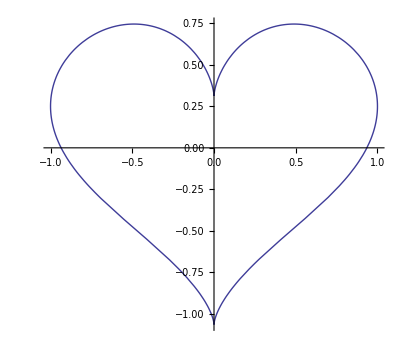

```mathematica
ParametricPlot[1/16{ 16 Sin[t]^3,13 Cos[t]-5 Cos[2 t]-2Cos[3t]-Cos[4t]},{t,0,2π}]
```

```mathematica
13 Cos[t]-5 Cos[2 t]-2Cos[3t]-Cos[4t]//TrigFactor
```

13 Cos[t]-5 Cos[2 t]-2 Cos[3 t]-Cos[4 t]

```mathematica
D[f[r,t]/a[r,t],r]
```

-(f[r,t] a^(1,0)[r,t])/a[r,t]^2+(f^(1,0)[r,t])/a[r,t]

```mathematica
x=f*Cosh[n]Cos[t]
y=f*Sinh[n]Sin[t]
D[x,{n,2}]==x
D[y,{n,2}]==y
```

f Cos[t] Cosh[n]

f Sin[t] Sinh[n]

True

True